```mathematica
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 15],ImageSize->Medium];

μ0 = 4π*10^-7;
cm = 100;
mm = 1000;
```

### Circular Coil for Quadrupole Coils

```mathematica
BzCircCoil[r_,z_,length_, radius_, turns_, amps_]:= Module[
{L=length, a=radius, t=turns, i=amps, n, B0,ζ1,ζ2,m1,m2,u}, 
(*Here, L is defined to be the solenoid length in z axis. So, this is not the length of the wire*)
n = t/L; (*# of wire turns per unit length of a solenoid*)
B0 = μ0 i n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/(4π)1/(√(a r))(√m1 ζ1(EllipticK[m1]+((a-r)/(a+r))EllipticPi[u,m1])-√m2 ζ2(EllipticK[m2]+((a-r)/(a+r))EllipticPi[u,m2]))];
BrCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2},
n = t/L;
B0 = μ0 i n;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/π √(a/r)(1/(√m1)(EllipticE[m1]-(1-m1/2)EllipticK[m1])-1/(√m2)(EllipticE[m2]-(1-m2/2)EllipticK[m2]))
];
```

```mathematica
(*independent variables*)
L=7/mm;(*length, m*)
a= 25/mm;(*minimum radius, m*)
dia=0.65/mm; (*wire dia, mm*)
t=Floor[L/dia+0.5];(*turns in 1 layer*)
amps=1;
layers = 12;
d =60/mm; (*center to center coil separation*)

Print["coil turns in 1 layer: ", t]
Print["# of layers: ",layers]
Print["Total # of layers: ",t*layers]
Print["Thickness of # layers: ", dia*layers*mm]
Print["Total wire length: ", N[t*layers*a*2*π]," m"]
```

coil turns in 1 layer: 11

# of layers: 12

Total # of layers: 132

Thickness of # layers: 7.8

Total wire length: 20.7345 m

Anti-Helmholtz configuration (for MOT)

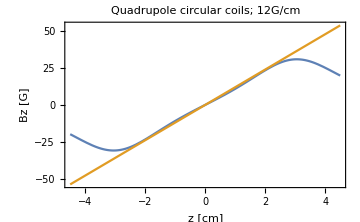

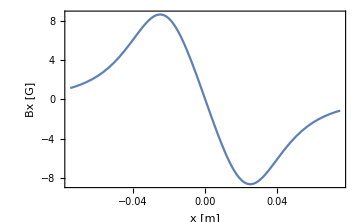

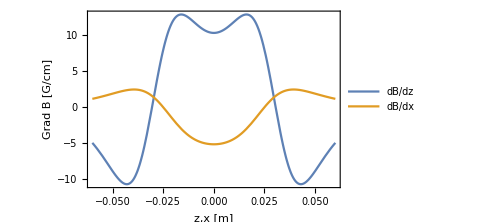

```mathematica
"Anti-Helmholtz configuration (for MOT)"
Bz=0;(*the field function*)
Br=0;
Bzlist = {};(*list for storing solenoid field for different number of turns, for debugging*)
Brlist={};
(*construct field from a pair of layered coils*)
For[i=1,i<layers+1,i++,
(*Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]; BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];*)
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
Br+=BrCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BrCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
]
(*Bx can be gotten by plotting sign(x)Br*)
Theory1=Plot[{10^4 Bz/.{r->10^-8,z->zcm/cm},12 zcm},{zcm,cm*-3d/4,cm*3d/4},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]","Bz [G]"},PlotLabel->"Quadrupole circular coils; 12G/cm"]

Plot[10^4 Sign[r]Br/.z->10^-8,{r,-3a,3a},PlotRange->All,FrameLabel->{"x [m]","Bx [G]"}]

Plot[{Evaluate[0.01D[10^4 Bz/.r->10^-8,z]/.z->x],Evaluate[0.01Sign[r]D[10^4 Br/.z->10^-8,r]/.r->x]},{x,-d,d},FrameLabel->{"z,x [m]","Grad B [G/cm]"},PlotLegends->{"dB/dz","dB/dx"}]

(*(*coil graphics - just a pair of lines representing a coil cross section*)
leftcoil ={ListPlot[{{-(d+L)/2,-a},{-(d-L)/2,-a}},PlotStyle->Blue,Joined->True],ListPlot[{{-(d+L)/2,a},{-(d-L)/2,a}},PlotStyle->Blue,Joined->True]};
rightcoil = {ListPlot[{{(d+L)/2,-a},{(d-L)/2,-a}},PlotStyle->Red,Joined->True],ListPlot[{{(d+L)/2,a},{(d-L)/2,a}},PlotStyle->Red,Joined->True]};

Show[VectorPlot[{10^4 Bz/.r->Abs[x],10^4 Sign[x]Br/.r->x},{z,-d,d},{x,0,2a},PlotLegends->Automatic,FrameLabel->{"z [m]","x [m]"},VectorPoints->Fine],leftcoil,rightcoil,Grid->True]*)
```

```mathematica
Print["Peak qud field [G] with ", amps," amps", " (1 coil on)"]
10^4 Bz/.{r->10^-8,z->d/2}
```

Peak qud field [G] with 1 amps (1 coil on)

29.8648

Helmholtz configuration (for bias field)

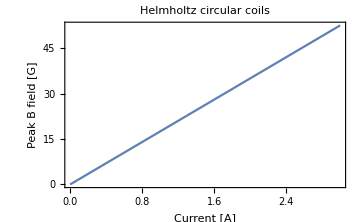

```mathematica
"Helmholtz configuration (for bias field)"
Bz=0;(*the field function*)
Br=0;
Bzlist = {};(*list for storing solenoid field for different number of turns, for debugging*)
Brlist={};
(*construct field from a pair of layered coils*)
Clear[amps]
For[i=1,i<layers+1,i++,
(*Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]; BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];*)
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,amps];
]
(*Bx can be gotten by plotting sign(x)Br*)
Plot[10^4 Bz/.{r->10^-8,z->0},{amps,0,3},FrameLabel->{"Current [A]", "Peak B field [G]"},PlotRange->All,PlotLabel->"Helmholtz circular coils"]
```

## Experimental Data Quadrupole

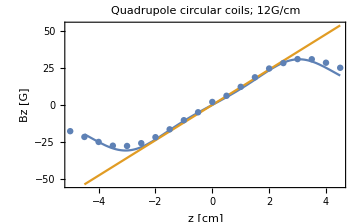

```mathematica
mLpR = {{19,17.85},{19.5,21.76},{20,25.15},{20.5,27.7},{21,27.9},{21.5,26},{22,21.93},{22.5,16.6},{23,10.4},{23.5,5},{24,-2},{24.5,-6.2},{25,-12.27},{25.5,-18.74},{26,-24.7},{26.5,-28.4},{27,-31.1},{27.5,-31},{28,-28.64},{28.5,-25.2}};
mLpR[[All,1]]=mLpR[[All,1]]-24;
mLpR[[All,2]]=-mLpR[[All,2]];
A1 = ListPlot[mLpR, PlotRange->{{-4,4},{-40,40}}];
Show[Theory1, A1]
```

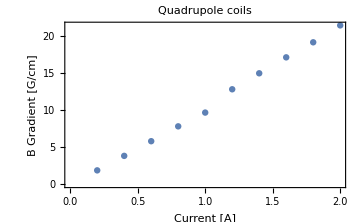

```mathematica
grad = {{0.2,1.886666667},{0.4,3.833333333},{0.6,5.805},{0.8,7.8},{1,9.65},{1.2,12.78},{1.4,14.92727273},{1.6,17.06909091},{1.8,19.09090909},{2,21.36363636}};
ListPlot[grad, FrameLabel->{"Current [A]", "B Gradient [G/cm]"},PlotLabel->"Quadrupole coils"]
```

```mathematica
(*Resistance of Copper wire*)
```

```mathematica
mm = 10^-3;
m = 1;
diameter = 0.65 *mm;
area = (diameter/2)^2*π;
length = 20 * m;
resistivity = 1.72*10^-8(*@ 20C*);
Resistance = resistivity * length / area;
Print["Resistance at 20C = ", Resistance]
```

Resistance at 20C = 1.03667

```mathematica
temp = 50;
Print["Resistance at ",temp,"C = ", Resistance + 0.00386*(temp-20)]
```

Resistance at 50C = 1.15247